## Lesson 19: Series solutions near a Regular singular point

## Overview

For the differential equation with functional coefficients:

P(x)y''(x)+Q(x)y'(x)+R(x)y(x)=0

an attempt will be made to solve for a series solution centered at x_0 where:

P(x_o)=0

You will find that the series solutions about a “regular” singular point take on a more general form of solutions to Euler equations:

y(x)=x^r∑_(n=0)^∞ a_n x^n

The solution method involves finding the roots of a higher-degree polynomial.

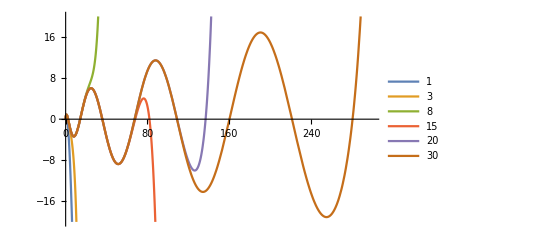

```mathematica
sln=Table[x (1+Sum[(-1)^n 2^n/Factorial[2n+1] x^n,{n,1,i}])+ √x(1+Sum[(-1)^n 2^n/Factorial[2n] x^n,{n,1,i}]),{i,{1,3,8,15,20,30}}];
Plot[sln,{x,0,300},PlotRange->{-20,20},PlotLegends->{1,3,8,15,20,30}]
```

## Regular Singular Point

The goal is to find a series solution for the equation:

P(x)y''(x)+Q(x)y'(x)+R(x)y(x)=0

where the series solution is centered at a regular singular point.

A regular singular point x_0 has the properties that:

P(x_o)=0

lim_(x→x_o) ((x-x_o)Q(x))/(P(x))            is finite

lim_(x→x_o) ((x-x_o)^2 R(x))/(P(x))          is finite

Assume without any loss of generality that the ODE has a regular singular point at x_0=0 and define similarly to ordinary points:

(x Q(x))/(P(x))=x p(x)

and

(x^2 R(x))/(P(x))=x^2 q(x)

## Example of a Regular Singular Point

Show that the following differential equation has a regular singular point at x_o=0:

9 x y''(x)+(1-x)y'(x)-y(x)=0

The appropriate functions can be defined using the following commands:

```mathematica
P[x_]:=9x
Q[x_]:=(1-x)
R[x_]:=-1
```

Now you can check to see that x_0=0 possesses all of the properties of a regular singular point:

```mathematica
P[0]
```

0

Check the limit using the following function:

```mathematica
Limit[x Q[x]/P[x],x->0]
```

1/9

The last property that needs to be verified follows:

```mathematica
Limit[x^2 R[x]/P[x],x->0]
```

0

## Simplifications

Because x_0=0 is assumed to be a regular singular point, both can be defined:

lim_(x→x_o) x p(x)=p_o

lim_(x→x_o) x^2 q(x)=q_o

Furthermore, because these functions are both analytic, they can be expressed as Taylor series:

x p(x)=∑_(n=0)^∞ p_n x^n

x^2 q(x)=∑_(n=0)^∞ q_n x^n

With these expressions, you can solve the equation by assuming the solution takes the form:

y(x)=x^r∑_(n=0)^∞ a_n x^n

## Example 1

Find a general solution for the following differential equation:

4 x y''(x)+2 y'(x)+y(x)=0

Begin by assuming that the solution takes the form:

y(x)=x^r∑_(n=0)^∞ a_n x^n

Then the derivatives can be calculated as:

```mathematica
sol=Sum[a[n] x^(r+n),{n,0,∞}];
```

```mathematica
y'[x]/.y->Function[x,Evaluate[sol]]
```

∑_(n=0)^∞ (n+r) x^(-1+n+r) a[n]

```mathematica
y''[x]/.y->Function[x,Evaluate[sol]]
```

∑_(n=0)^∞ (-1+n+r) (n+r) x^(-2+n+r) a[n]

## Example 1

Inserting this into the equation, you find that:

```mathematica
(4x y''[x]+2y'[x]+y[x]==0)/.y->Function[x,Evaluate[sol]]
```

4 x ∑_(n=0)^∞ (-1+n+r) (n+r) x^(-2+n+r) a[n]+2 ∑_(n=0)^∞ (n+r) x^(-1+n+r) a[n]+∑_(n=0)^∞ x^(n+r) a[n]==0

What is required now is to make some transformations to find a more simplified answer.

First, combine the first two summations into one summation:

∑_(n=0)^∞ (4(-1+n+r)(n+r)+2(n+r))x^(-1+n+r)a[n]+∑_(n=0)^∞ x^(n+r)a[n]=0

## Example 1

Change the index of the second summation and simplify the first term:

∑_(n=0)^∞ 2 a[n](r+n)(2r+2n-1)x^(-1+n+r)+∑_(n=1)^∞ x^(n+r-1)a[n-1]=0

Factor out the first term of the first summation:

2 a[0]r(2r-1)x^(r-1)+∑_(n=1)^∞ 2 a[n](r+n)(2r+2n-1)x^(-1+n+r)+∑_(n=1)^∞ x^(n+r-1)a[n-1]=0

Combine the two summations into a single summation:

2 a[0]r(2r-1)x^(r-1)+∑_(n=1)^∞ (2 a[n](r+n)(2r+2n-1)+a[n-1])x^(n+r-1)=0

Now the series solution can be decomposed into two equations:

2 a_o r (2r-1)x^(r-1)=0

2 a_n(r+n)(2r+2n-1)+a_(n-1)=0

## Example 1

The series solution has been decomposed into two equations:

2 a_o r (2r-1)x^(r-1)=0

2 a_n(r+n)(2r+2n-1)+a_(n-1)=0

Solve the first equations to find the solutions r=0 and r=1/2:

```mathematica
Solve[2 Subscript[a, o] r(2r-1)x^(r-1)==0,r]
```

{{r→0},{r→1/2}}

You must solve the recurrence relation for both of these values.

When r=0, the recurrence relation you must solve is:

a[n]=-a[n-1]/(2 n (2 n-1))

The series coefficients can be seen to be:

a_0,-a_0/(2!), a_0/(4!), -a_0/(6!),...

Thus the solution corresponding with this value for r is a_0 cos(√x):

```mathematica
Series[Cos[Sqrt[x]],{x,0,5}]
```

1-x/2+x^2/24-x^3/720+x^4/40320-x^5/3628800+O[x]^6

## Example 1

For the case of r=1/2, the recurrence relation becomes:

a[n]=-a[n-1]/(2n (2n+1))

The series coefficients can be seen to be:

a_0-a_0/(3!), a_0/(5!), -a_0/(7!),...

Thus the solution corresponding with this value for r is a_0 sin(√x).

Now you have found two solutions to the differential equation, namely:

c_1 cos(√x)

c_2 sin(√x)

The solution can be verified using DSolveValue:

```mathematica
DSolveValue[4x y''[x]+2y'[x]+y[x]==0,y[x],x]
```

C[1] Cos[√x]+C[2] Sin[√x]

The solution in a series form can be found with AsymptoticDSolveValue:

```mathematica
AsymptoticDSolveValue[4x y''[x]+2y'[x]+y[x]==0,y[x],{x,0,5}]
```

√x (1-x/6+x^2/120-x^3/5040+x^4/362880-x^5/39916800) C[1]+(1-x/2+x^2/24-x^3/720+x^4/40320-x^5/3628800) C[2]

## Example 2

Find a general solution for the differential equation:

2 x^2 y''(x)-x y'(x)+(1+x)y(x)=0

Begin by assuming that the solution takes the form as before:

```mathematica
sol=Sum[a[n] x^(r+n),{n,0,∞}];
```

Inserting this into the equation, you find that:

```mathematica
(2 x^2*y''[x]-x*y'[x]+(1+x)y[x]==0)/.y->Function[x,Evaluate[sol]]
```

2 x^2 ∑_(n=0)^∞ (-1+n+r) (n+r) x^(-2+n+r) a[n]-x ∑_(n=0)^∞ (n+r) x^(-1+n+r) a[n]+(1+x) ∑_(n=0)^∞ x^(n+r) a[n]==0

Similar to the previous example, you can simplify the summations into the form:

a[0](2r(r-1)-r+1)x^r+∑_(n=1)^∞ ((2(r+n)(r+n-1)-(r+n)+1)a[n]+a[n-1])x^(r+n)=0

## Example 3

Then there are two equations:

2r(r-1)-r+1=0

(2(r+n)(r+n-1)-(r+n)+1)a[n]+a[n-1]=0

The first equation has solutions r=1 and r=1/2:

```mathematica
Solve[2 r(r-1)-r+1==0]
```

{{r→1/2},{r→1}}

Thus it is necessary to solve for the two corresponding solutions for each value of r.

When r=1, the second equation becomes:

a[n]=-(a[n-1]/n(2n+1))

This follows the pattern:

a_0,a_0/(3*1),a_0/(5*3*2*1),a_0/(7*5*3*3*2*1)

You can determine that the general term of the sequence is:

a_n=(-1)^n 2^n/((2n+1)!)a_0

Hence there is the first series solution:

y_1(x)=x(1+∑_(n=1)^∞ ((-1)^n 2^n)/((2n+1)!)x^n)

## Example 4

When r=1/2, the second equation becomes:

a[n]=-a[n-1]/(n(2n-1))

This follows the pattern:

a_0,a_0/(1*1),a_0/(1*2*1*3),a_0/(1*2*3*1*3*5)

You can determine that the general term of the sequence is:

a_n = (-1)^n 2^n/((2n)!)a_0

Hence the second series solution becomes:

y_2(x)=x^(1/2)(1+∑_(n=1)^∞ ((-1)^n 2^n)/((2n)!)x^n)

Thus, a general solution to the differential equation is:

y(x)=c_1 y_1(x)+c_2 y_2(x)

## Example 5

This solution has no recognizable closed form, so simply leave it in its series form.

You can solve this problem in an automated fashion by using the command AsymptoticDSolveValue:

```mathematica
AsymptoticDSolveValue[2 x^2 y''[x]-x y'[x]+(1+x)y[x]==0,y[x],{x,0,5}]
```

x (1-x/3+x^2/30-x^3/630+x^4/22680-x^5/1247400) C[1]+√x (1-x+x^2/6-x^3/90+x^4/2520-x^5/113400) C[2]

It can be observed that this is equal to the solution obtained through manual calculations:

```mathematica
Subscript[C, 1] x(1+Sum[(-1)^n 2^n/Factorial[2n+1] x^n,{n,1,5}])+ Subscript[C, 2] √x(1+Sum[(-1)^n 2^n/Factorial[2n] x^n,{n,1,5}])
```

x (1-x/3+x^2/30-x^3/630+x^4/22680-x^5/1247400) C_1+√x (1-x+x^2/6-x^3/90+x^4/2520-x^5/113400) C_2

Visualize the solution with an increasing number of terms using 𝕔_1=𝕔_2=1:

```mathematica
sln=Table[x (1+Sum[(-1)^n 2^n/Factorial[2n+1] x^n,{n,1,i}])+ √x(1+Sum[(-1)^n 2^n/Factorial[2n] x^n,{n,1,i}]),{i,{1,3,8,15,20,30}}];
Plot[sln,{x,0,300},PlotRange->{-20,20},PlotLegends->{1,3,8,15,20,30}]
```

-Graphics-

## Summary

In this lesson, the theory of infinite series was used to construct a solution to a differential equation that has a regular singular point.

The solutions take a form similar to that of Euler equations:

y(x)=x^r∑_(n=0)^∞ a_n x^n

Thus in order to find the series solution, it is necessary to determine the value of r, the recurrence relation of a_n and the radius of convergence for:

∑_(n=0)^∞ a_n x^n

Some of the classical functions that solve these differential equations will be explored.